# Check our Fortan implementation of EMT

## We are sure that our implementation is right. If you doubt us, screw u.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/MPG-BPC/akandra/git/mdhag/pes_fitting_programs/EMT_potential

```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot};
```

```mathematica
pbc[r_,celldim_]:=r-celldim Round[r/celldim]
```

```mathematica
δf[x_,psrules_,pars_]:={x,x/.psrules}/.pars
relab[δf_]:=1-δf[[2]]/δf[[1]]
```

```mathematica
cell={{17.82333, 0.00000, 0.00000},{-8.91167, 15.43546,0.00000},{0.00000, 0.00000, 20.25730}};
```

```mathematica
cell//MatrixForm
```

(17.8233 | 0. | 0.
-8.91167 | 15.4355 | 0.
0. | 0. | 20.2573)

```mathematica
Inverse[cell]//MatrixForm
```

(0.0561062 | 0. | 0.
0.032393 | 0.0647859 | 0.
0. | 0. | 0.0493649)

```mathematica
x={0,22.27917,0}
```

{0,22.2792,0}

```mathematica
cell.(Inverse[cell].x-Round[Inverse[cell].x])
```

{0.,6.84371,0.}

```mathematica
Inverse[cell][[1,1]]x[[1]]
Inverse[cell][[2,1]]x[[1]]+Inverse[cell][[2,2]]x[[2]]
Inverse[cell][[3,3]]x[[3]]
```

-0.0833335

-0.881446

0.

## Equilibrium configuration

#### Import Fit Data and define geometry

read in the positions of the lattice and h atoms

```mathematica
data=Import["ref_conf_Au111.dat"];data=Import["../Fit_with_static_lattice/derivatives/reindeer.dat"];
dataH=Import["hau111_plot.E.dat"];
rAu=data[[7;;]];
rHsrules=MapThread[#1->#2&,{{x,y,z},#}]&/@dataH[[All, 2;;4]];
```

configure positions of atoms for operation

```mathematica
nAu=Length[rAu]
nlayer=data[[2,1]]
nperl=nAu/nlayer
dnn=data[[3,1]]
celldim=data[[{4,5},1]]
```

144

4

36

2.97056

{17.8233,15.4355}

Gets the Geometries set. Again, we get ‘periodic boundary conditions’ by acting as if the atom in the middle of each layer is the same as each other atom of that layer.

```mathematica
rAul=Table[rAu[[1+4(i-1)]],{i,nlayer}];
rrAuAu=Table[Select[Norm[#-rAul[[i]]]&/@rAu,#>0&],{i,nlayer}];
rrHAu=Table[√(({x,y,z}-rAu[[j]]).({x,y,z}-rAu[[j]])),{j,nAu}];
rpl=(rrHAu/.rHsrules)ᵀ;
```

#### Read in potential parameters

```mathematica
β=(16π/3)^(1/3)/(√2);
bohr=0.5291772082952705
```

0.529177

Fit paramters, fit 89

```mathematica
{η2H, noH, eoH,λH,voH, κH, soH}=Import["/home/MPG-BPC/akandra/Dropbox/trial17/stroem_der.89.H.nml", "Table"][[3;;-2,2]];
{η2Au, noAu, eoAu,λAu,voAu, κAu, soAu}=Import["/home/MPG-BPC/akandra/Dropbox/trial17/stroem_der.89.Au.nml", "Table"][[3;;-2,2]];
paars89={η2l->η2Au,κl->κAu,λl->λAu,eol->eoAu,sol->soAu,vol->voAu,nol->noAu,η2p->η2H,κp->κH,λp->λH,eop->eoH,sop->soH,vop->voH,nop->noH}
```

{η2l→3.66676,κl→5.15268,λl→4.93867,eol→-3.8,sol→1.64174,vol→2.321,nol→0.0245573,η2p→1.577,κp→3.3728,λp→1.74377,eop→-2.371,sop→0.680411,vop→0.145531,nop→0.207337}

Fit paramters, fit 90

```mathematica
{η2H, noH, eoH,λH,voH, κH, soH}=Import["/home/MPG-BPC/akandra/Dropbox/trial17/stroem_der.90.H.nml", "Table"][[3;;-2,2]];
{η2Au, noAu, eoAu,λAu,voAu, κAu, soAu}=Import["/home/MPG-BPC/akandra/Dropbox/trial17/stroem_der.90.Au.nml", "Table"][[3;;-2,2]];
paars90={η2l->η2Au,κl->κAu,λl->λAu,eol->eoAu,sol->soAu,vol->voAu,nol->noAu,η2p->η2H,κp->κH,λp->λH,eop->eoH,sop->soH,vop->voH,nop->noH}
```

{η2l→4.08935,κl→7.39677,λl→0.419986,eol→-3.8,sol→1.64174,vol→2.321,nol→0.0198843,η2p→1.27639,κp→2.35467,λp→1.43504,eop→-2.371,sop→0.680411,vop→0.852378,nop→0.253102}

Fit paramters, fit 119

```mathematica
{η2H, κH, λH,eoH,soH, voH, noH}=Import["parameters_H_f119.nml", "Table"][[3;;-2,2]];
{η2Au, κAu, λAu,eoAu,soAu, voAu, noAu}=Import["parameters_Au_f119.nml", "Table"][[3;;-2,2]];
paars119={η2l->η2Au,κl->κAu,λl->λAu,eol->eoAu,sol->soAu,vol->voAu,nol->noAu,η2p->η2H,κp->κH,λp->λH,eop->eoH,sop->soH,vop->voH,nop->noH}
```

{η2l→3.84357,κl→6.59507,λl→4.12338,eol→-3.8,sol→1.64174,vol→2.321,nol→0.017325,η2p→1.58126,κp→2.97711,λp→1.76764,eop→-2.371,sop→0.680411,vop→0.667655,nop→0.295577}

Fit paramters, Strömqvist

```mathematica
{η2H, noH,eoH,λH,voH,κH,soH}=Import["../Fit_with_static_lattice/derivatives/data/parameters_and_fit_results/stroem.00.H.nml", "Table"][[3;;-2,2]];
{η2Au, noAu,eoAu,λAu, voAu, κAu,soAu}=Import["../Fit_with_static_lattice/derivatives/data/parameters_and_fit_results/stroem.00.Au.nml", "Table"][[3;;-2,2]];
paarsS={η2l->η2Au,κl->κAu,λl->λAu,eol->eoAu,sol->soAu,vol->voAu,nol->noAu,η2p->η2H,κp->κH,λp->λH,eop->eoH,sop->soH,vop->voH,nop->noH}
```

{η2l→3.1634,κl→5.42918,λl→4.12338,eol→-3.8,sol→1.64174,vol→2.321,nol→0.0474408,η2p→5.4254,κp→8.86282,λp→7.72709,eop→-2.371,sop→0.680411,vop→0.427,nop→0.182205}

#### Derivatives for χ

In our Fortran program, they form an array in which the first element corresponds to the derivative with respect to nop and the second to the derivative with respect to nol

```mathematica
χlp = nop/nol;
D[χlp,#]&/@{nop,nol}
{χlp,%}/.paars90
```

{1/nol,-nop/nol^2}

{12.7287,{50.291,-640.14}}

```mathematica
%[[2]]/%[[1]]
```

{3.95098,-50.291}

```mathematica
χpl = nol/nop;
D[χpl,#]&/@{nop,nol}
{χpl,%}/.paarsS
```

{-nol/nop^2,1/nop}

{0.26037,{-1.429,5.48832}}

```mathematica
%[[2]]/%[[1]]
```

{-5.48832,21.0789}

#### Gamma

Is used to enact the cut-off. We regard this part of the equation as derivative free -- for the fit.

```mathematica
Log[9999.]
```

9.21024

```mathematica
rc=5.14515;
rr= (4rc)/(√3+2);
acut=Log[9999]/(rr-rc);
rAunn=Table[soAu β √i,{i,3} ]
rHnn=Table[soH β √i,{i,3} ]
```

{2.97056,4.20101,5.14517}

{1.23114,1.74109,2.13239}

```mathematica
xAu1=1/(1+Exp[acut(rAunn[[1]]-rc)]);
xAu2=1/(2(1+Exp[acut(rAunn[[2]]-rc)]));
xAu3=2/(1+Exp[acut(rAunn[[3]]-rc)]);
xAu=List[xAu1,xAu2,xAu3];
xH1=1/(1+Exp[acut(rHnn[[1]]-rc)]);
xH2=1/(2(1+Exp[acut(rHnn[[2]]-rc)]));
xH3=2/(1+Exp[acut(rHnn[[3]]-rc)]);
xH=List[xH1,xH2,xH3];
```

```mathematica
N[Sqrt[0.5],10]
xAu
xH
```

0.707107

{1.,0.5,0.999778}

{1.,0.5,2.}

```mathematica
γ1l=Total[xAu Exp[-η2l(rAunn-β sol)]];
γ2l=Total[xAu Exp[-κl/β(rAunn-β sol)]];
γ1p=Total[xH Exp[-η2p(rHnn-β sop)]];
γ2p=Total[xH Exp[-κp/β(rHnn-β sop)]];
```

```mathematica
{γ1l,γ2l,γ1p,γ2p}^(-1) /.paars90
```

{0.99661,0.996604,0.528027,0.53292}

```mathematica
{{D[γ1l,η2l],D[γ1l,sol]},{D[γ2l,κl],D[γ2l,sol]},{D[γ1p,η2p],D[γ1p,sop]},{D[γ2p,κp],D[γ2p,sop]}}/.paars90
```

{{-0.00431454,7.42444},{-0.00238881,7.42197},{-0.703531,4.37382},{-0.380874,4.41844}}

```mathematica
%/%%
```

{{-0.00432921,7.44969},{-0.00239695,7.44725},{-1.33238,8.28332},{-0.714692,8.291}}

#### Theta. Part of the cut-off, has also no derivative.

```mathematica
xσAuAu=Table[Exp[acut(rrAuAu[[i]]-rc)],{i,nlayer}];
xσHAu=Exp[acut(rpl-rc)];
θAuAu=Table[1/(1+xσAuAu[[i]]),{i,nlayer}];
θHAu=1/(1+xσHAu);
```

#### Derivatives of σ

```mathematica
σll=Table[Total[Exp[-η2l (rrAuAu[[i]]-β sol)] θAuAu[[i]]/γ1l],{i,nlayer}];
σlp=Exp[-η2p(rpl-β sop)] θHAu/γ1l;
σpl=Total[Exp[-η2l(rpl-β sol)] θHAu/γ1p];
```

```mathematica
σll/.paars90
```

{8.85746,12.2172,12.3363,8.97663}

```mathematica
{D[σll,η2l],D[σll,sol]}/.paars90
```

{{-0.0191537,0.0584712,0.086716,0.00891267},{2.84217×10^-14,4.26326×10^-14,4.26326×10^-14,2.84217×10^-14}}

```mathematica
%ᵀ/%%
```

{{-0.00216243,3.20879×10^-15},{0.00478596,3.48954×10^-15},{0.00702932,3.45586×10^-15},{0.000992875,3.16619×10^-15}}

```mathematica
{σlp[[All,55]],σpl[[55]]}/.paars90//Chop
```

{{2.37189×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},0}

```mathematica
{D[σlp[[All,55]],η2l],D[σpl[[55]],η2l]}/.paars90//Chop
{D[σlp[[All,55]],η2p],D[σpl[[55]],η2p]}/.paars90//Chop
{D[σlp[[All,55]],sol],D[σpl[[55]],sol]}/.paars90//Chop
{D[σlp[[All,55]],sop],D[σpl[[55]],sop]}/.paars90//Chop
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},0}

{{-1.08368×10^-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},0}

{{-1.75503×10^-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},0}

{{5.47787×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},0}

#### Derivatives of ds

```mathematica
dsl=-1/(β η2l)Table[Log[(σll[[1+Quotient[Mod[i,16,1]-1,4]]]+χlp σlp[[i]])/12],{i,nAu}];
```

```mathematica
dsp=-Log[(χpl σpl)/12]/(β η2p);
```

```mathematica
{dsl[[All,55]],dsp[[55]]}/.paars90
```

{{0.0410374,0.0410374,0.0410374,0.0410374,-0.00242469,-0.00242469,-0.00242469,-0.00242469,-0.00373561,-0.00373561,-0.00373561,-0.00373561,0.0392312,0.0392312,0.0392312,0.0392312,0.0410374,0.0410374,0.0410374,0.0410374,-0.00242469,-0.00242469,-0.00242469,-0.00242469,-0.00373561,-0.00373561,-0.00373561,-0.00373561,0.0392312,0.0392312,0.0392312,0.0392312,0.0410374,0.0410374,0.0410374,0.0410374,-0.00242469,-0.00242469,-0.00242469,-0.00242469,-0.00373561,-0.00373561,-0.00373561,-0.00373561,0.0392312,0.0392312,0.0392312,0.0392312,0.0410374,0.0410374,0.0410374,0.0410374,-0.00242469,-0.00242469,-0.00242469,-0.00242469,-0.00373561,-0.00373561,-0.00373561,-0.00373561,0.0392312,0.0392312,0.0392312,0.0392312,0.0410374,0.0410374,0.0410374,0.0410374,-0.00242469,-0.00242469,-0.00242469,-0.00242469,-0.00373561,-0.00373561,-0.00373561,-0.00373561,0.0392312,0.0392312,0.0392312,0.0392312,0.0410374,0.0410374,0.0410374,0.0410374,-0.00242469,-0.00242469,-0.00242469,-0.00242469,-0.00373561,-0.00373561,-0.00373561,-0.00373561,0.0392312,0.0392312,0.0392312,0.0392312,0.0410374,0.0410374,0.0410374,0.0410374,-0.00242469,-0.00242469,-0.00242469,-0.00242469,-0.00373561,-0.00373561,-0.00373561,-0.00373561,0.0392312,0.0392312,0.0392312,0.0392312,0.0410374,0.0410374,0.0410374,0.0410374,-0.00242469,-0.00242469,-0.00242469,-0.00242469,-0.00373561,-0.00373561,-0.00373561,-0.00373561,0.0392312,0.0392312,0.0392312,0.0392312,0.0410374,0.0410374,0.0410374,0.0410374,-0.00242469,-0.00242469,-0.00242469,-0.00242469,-0.00373561,-0.00373561,-0.00373561,-0.00373561,0.0392312,0.0392312,0.0392312,0.0392312},14.5335}

```mathematica
{D[dsl[[All,55]],η2l],D[dsl[[All,55]],nol],D[dsl[[All,55]],sol]}/.paars90//Chop
```

{{-0.00974293,-0.00974293,-0.00974293,-0.00974293,-0.000053888,-0.000053888,-0.000053888,-0.000053888,-0.0000365059,-0.0000365059,-0.0000365059,-0.0000365059,-0.00972767,-0.00972767,-0.00972767,-0.00972767,-0.00974293,-0.00974293,-0.00974293,-0.00974293,-0.000053888,-0.000053888,-0.000053888,-0.000053888,-0.0000365059,-0.0000365059,-0.0000365059,-0.0000365059,-0.00972767,-0.00972767,-0.00972767,-0.00972767,-0.00974293,-0.00974293,-0.00974293,-0.00974293,-0.000053888,-0.000053888,-0.000053888,-0.000053888,-0.0000365059,-0.0000365059,-0.0000365059,-0.0000365059,-0.00972767,-0.00972767,-0.00972767,-0.00972767,-0.00974293,-0.00974293,-0.00974293,-0.00974293,-0.000053888,-0.000053888,-0.000053888,-0.000053888,-0.0000365059,-0.0000365059,-0.0000365059,-0.0000365059,-0.00972767,-0.00972767,-0.00972767,-0.00972767,-0.00974293,-0.00974293,-0.00974293,-0.00974293,-0.000053888,-0.000053888,-0.000053888,-0.000053888,-0.0000365059,-0.0000365059,-0.0000365059,-0.0000365059,-0.00972767,-0.00972767,-0.00972767,-0.00972767,-0.00974293,-0.00974293,-0.00974293,-0.00974293,-0.000053888,-0.000053888,-0.000053888,-0.000053888,-0.0000365059,-0.0000365059,-0.0000365059,-0.0000365059,-0.00972767,-0.00972767,-0.00972767,-0.00972767,-0.00974293,-0.00974293,-0.00974293,-0.00974293,-0.000053888,-0.000053888,-0.000053888,-0.000053888,-0.0000365059,-0.0000365059,-0.0000365059,-0.0000365059,-0.00972767,-0.00972767,-0.00972767,-0.00972767,-0.00974293,-0.00974293,-0.00974293,-0.00974293,-0.000053888,-0.000053888,-0.000053888,-0.000053888,-0.0000365059,-0.0000365059,-0.0000365059,-0.0000365059,-0.00972767,-0.00972767,-0.00972767,-0.00972767,-0.00974293,-0.00974293,-0.00974293,-0.00974293,-0.000053888,-0.000053888,-0.000053888,-0.000053888,-0.0000365059,-0.0000365059,-0.0000365059,-0.0000365059,-0.00972767,-0.00972767,-0.00972767,-0.00972767},{2.31671×10^-9,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{3.40855×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
%ᵀ/%%[[1]]
```

{{-0.237416,5.64536×10^-8,8.30597×10^-9},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{-0.237416,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0222247,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{0.0097724,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.},{-0.247958,0.,0.}}

```mathematica
{D[dsl[[All,55]],η2p],D[dsl[[All,55]],nop],D[dsl[[All,55]],sop]}/.paars90//Chop
```

{{2.1047×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1.82006×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1.06389×10^-10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
{D[dsp[[55]],η2l],D[dsp[[55]],nol],D[dsp[[55]],sol]}/.paars90//Chop
{D[dsp[[55]],η2p],D[dsp[[55]],nop],D[dsp[[55]],sop]}/.paars90//Chop
```

{1.22513,-21.7758,-3.20385}

{-11.5473,1.71076,1.}

#### Derivatives of Pair Potentials

```mathematica
vll=-vol/2 nperl Total[  Exp[-κl(Flatten[rrAuAu]/β- sol)] Flatten[θAuAu]/γ2l];
vlp=-vol/2 χlp Total[Exp[-κp (rpl/β- sop)] θHAu/γ2l];
vpl=-vop/2 χpl Total[Exp[-κl (rpl/β- sol)] θHAu/γ2p];
```

```mathematica
vll/.paars90
{D[vll,κl],D[vll,sol],D[vll,vol]}/.paars90
```

-1770.86

{-3.11664,0.,-762.974}

```mathematica
{vlp[[1]],vpl[[1]]}/.paars90
```

{-39.2511,-9.14406}

```mathematica
{D[vlp[[1]],nol],D[vlp[[1]],nop]}/.paars90
{D[vpl[[1]],nol],D[vpl[[1]],nop]}/.paars90
```

{1973.97,-155.08}

{-459.864,36.128}

```mathematica
{D[vlp[[1]],vol],D[vlp[[1]],vop]}/.paars90
{D[vpl[[1]],vol],D[vpl[[1]],vop]}/.paars90
```

{-16.9113,0}

{0,-10.7277}

```mathematica
{D[vlp[[1]],κl],D[vlp[[1]],κp]}/.paars90
{D[vpl[[1]],κl],D[vpl[[1]],κp]}/.paars90
```

{-0.0934448,24.347}

{-6.16708,-1.85602}

```mathematica
{D[vlp[[1]],sol],D[vlp[[1]],sop]}/.paars90
{D[vpl[[1]],sol],D[vpl[[1]],sop]}/.paars90
```

{290.331,-92.4234}

{-67.6365,21.5313}

#### Derivatives of Reference Pair Potentials

```mathematica
vrefl= 6vol Total[Exp[-κl dsl]];
vrefp=6vop Exp[-κp dsp];
```

```mathematica
{vrefl[[55]],vrefp[[55]]}/.paars90
```

{1770.94,7.02242×10^-15}

```mathematica
{D[vrefl[[1]],η2l],D[vrefl[[1]],nol],D[vrefl[[1]],vol],D[vrefl[[1]],κl],D[vrefl[[1]],sol]}/.paars90
```

{43.0298,-2029.72,780.396,-20.5776,-298.631}

```mathematica
{D[vrefl[[1]],η2p],D[vrefl[[1]],nop],D[vrefl[[1]],vop],D[vrefl[[1]],κp],D[vrefl[[1]],sop]}/.paars90
```

{-46.1058,159.459,0,0,93.2099}

```mathematica
{D[vrefp[[1]],η2l],D[vrefp[[1]],nol],D[vrefp[[1]],sol]}/.paars90
```

{11.4194,470.594,69.2382}

```mathematica
{D[vrefp[[1]],η2p],D[vrefp[[1]],nop],D[vrefp[[1]],vop],D[vrefp[[1]],κp],D[vrefp[[1]],sop]}/.paars90
```

{-0.728609,-36.971,10.7674,2.27924,-21.6109}

#### Derivatives of Ecoh

```mathematica
ecohl=Total[eol((1+λl dsl)Exp[-λl dsl]-1)];
ecohp=eop((1+λp dsp)Exp[-λp dsp]- 1 0);
```

```mathematica
ecohl[[55]]/.paars90
```

0.0386921

```mathematica
ecoh=ecohl[[55]]+ecohp[[55]];
```

```mathematica
ecoh/.paars90
```

0.038692

```mathematica
{D[ecoh,η2l],D[ecoh,nol],D[ecoh,eol],D[ecoh,λl],D[ecoh,vol],D[ecoh,κl],D[ecoh,sol]}/.paars90
```

{-0.0185345,-1.3529×10^-6,-0.0101821,0.183226,0,0,-1.99052×10^-7}

```mathematica
{D[ecoh,η2p],D[ecoh,nop],D[ecoh,eop],D[ecoh,λp],D[ecoh,vop],D[ecoh,κp],D[ecoh,sop]}/.paars90
```

{-7.17448×10^-7,1.06287×10^-7,1.91363×10^-8,6.29246×10^-7,0,0,6.21288×10^-8}

#### Final Derivatives

```mathematica
eemm=ecohl+ecohp+vll+vlp+vpl+ 6vol Total[Exp[-κl dsl]]+ 6vop Exp[-κp dsp];
```

```mathematica
nt=55;
```

```mathematica
paars89
paars90
```

{η2l→3.66676,κl→5.15268,λl→4.93867,eol→-3.8,sol→1.64174,vol→2.321,nol→0.0245573,η2p→1.577,κp→3.3728,λp→1.74377,eop→-2.371,sop→0.680411,vop→0.145531,nop→0.207337}

{η2l→4.08935,κl→7.39677,λl→0.419986,eol→-3.8,sol→1.64174,vol→2.321,nol→0.0198843,η2p→1.27639,κp→2.35467,λp→1.43504,eop→-2.371,sop→0.680411,vop→0.852378,nop→0.253102}

```mathematica
eemm[[nt]]/.{η2l->4.08935,λl->0.419986}/. {paars89,paars90}
```

{71.9037,0.113435}

```mathematica
{D[eemm[[nt]],η2l],D[eemm[[nt]],nol],D[eemm[[nt]],eol],D[eemm[[nt]],λl],D[eemm[[nt]],vol],D[eemm[[nt]],κl],D[eemm[[nt]],sol]};
%/.{paars89,paars90}
```

{{47.6005,-4.04695×10^-6,-1.52872,2.18336,22.6632,-37.6674,-6.59596×10^-7},{53.9817,-1.37186×10^-6,-0.0101821,0.183226,0.0323097,-29.8553,-2.01843×10^-7}}

```mathematica
{D[eemm[[nt]],η2p],D[eemm[[nt]],nop],D[eemm[[nt]],eop],D[eemm[[nt]],λp],D[eemm[[nt]],vop],D[eemm[[nt]],κp],D[eemm[[nt]],sop]};
%/.{paars89,paars90}
```

{{-2.03535×10^-6,4.79327×10^-7,7.18927×10^-8,1.80996×10^-6,-9.7154×10^-13,3.9496×10^-10,2.83498×10^-7},{-7.33452×10^-7,1.07777×10^-7,1.91363×10^-8,6.29246×10^-7,-7.85808×10^-15,7.89304×10^-9,6.28581×10^-8}}

#### Reference energy

```mathematica
eemm0check=eemm-eemmref;
```

```mathematica
{D[eemm0check[[1]],η2p],D[eemm0check[[1]],nop],D[eemm0check[[1]],eop],D[eemm0check[[1]],λp],D[eemm0check[[1]],vop],D[eemm0check[[1]],κp],D[eemm0check[[1]],sop]}/. subruls
```

```mathematica
{-34.199497895566154,-1.4306274801689753,0.9983766983829074,0.004436343593595016,1.3264926855519565,18.056882681393613,-5.113597458586161}
```

```mathematica
{D[eemm0check[[1]],η2l],D[eemm0check[[1]],nol],D[eemm0check[[1]],eol],D[eemm0check[[1]],λl],D[eemm0check[[1]],vol],D[eemm0check[[1]],κl],D[eemm0check[[1]],sol]}/. subruls
```

{-5.97126,24.4075,-0.177676,0.359016,-0.0520612,4.18576,-9.15915}

strömqvist

```mathematica
{D[eemm0check[[1]],η2p],D[eemm0check[[1]],nop],D[eemm0check[[1]],eop],D[eemm0check[[1]],λp],D[eemm0check[[1]],vop],D[eemm0check[[1]],κp],D[eemm0check[[1]],sop]}/. paars
```

{-2.88483,-28.2334,0.0431287,0.79449,1.57829,1.18827,-56.2452}

```mathematica
{D[eemm0check[[1]],η2l],D[eemm0check[[1]],nol],D[eemm0check[[1]],eol],D[eemm0check[[1]],λl],D[eemm0check[[1]],vol],D[eemm0check[[1]],κl],D[eemm0check[[1]],sol]}/. paars
```

{14.0557,108.436,-0.000378037,0.000700446,-0.142487,-4.5563,31.2199}

## AIMD configuration

### Energy

#### Import Fit Data and define geometry

read in the positions of the lattice and h atoms

```mathematica
data=Import["../Fit_with_static_lattice/derivatives/aimdreindeer.dat"];
dataH=data[[8]]
rAu=data[[9;;]];
rHsrules=MapThread[#1->#2&,{{x,y,z},#}]&/@{dataH};
```

{0.55132,4.32308,1.89133}

configure positions of atoms for operation

```mathematica
nAu=Length[rAu]
nlayer=data[[2,1]]
nperl=nAu/nlayer
dnn=data[[3,1]]
celldim=data[[{4,5,6},1]]
```

144

4

36

2.97056

{17.8233,15.4355,20.2573}

Gets the Geometries set. Again, we get ‘periodic boundary conditions’ by acting as if the atom in the middle of each layer is the same as each other atom of that layer.

```mathematica
rrAuAu=Table[Norm[pbc[rAu[[i]]-rAu[[j]],celldim]],{i, nAu},{j,nAu}];
rpl=Table[Norm[pbc[dataH-rAu[[i]],celldim]],{i, nAu}];
```

#### Read in potential parameters (_not_ fitting parameters)

```mathematica
β=(16π/3)^(1/3)/(√2);
bohr=0.5291772082952705
```

0.529177

Fit paramters, fit 119

```mathematica
{η2H, κH, λH,eoH,soH, voH, noH}=Import["parameters_H_f119.nml", "Table"][[3;;-2,2]];
{η2Au, κAu, λAu,eoAu,soAu, voAu, noAu}=Import["parameters_Au_f119.nml", "Table"][[3;;-2,2]];
subruls={η2l->η2Au,κl->κAu,λl->λAu,eol->eoAu,sol->soAu,vol->voAu,nol->noAu,η2p->η2H,κp->κH,λp->λH,eop->eoH,sop->soH,vop->voH,nop->noH};
```

Fit paramters, Strömqvist

```mathematica
{η2H, noH,eoH,λH,voH,κH,soH}=Import["../Fit_with_static_lattice/derivatives/data/parameters_and_fit_results/stroem.00.H.nml", "Table"][[3;;-2,2]]
{η2Au, noAu,eoAu,λAu, voAu, κAu,soAu}=Import["../Fit_with_static_lattice/derivatives/data/parameters_and_fit_results/stroem.00.Au.nml", "Table"][[3;;-2,2]]
paars={η2l->η2Au,κl->κAu,λl->λAu,eol->eoAu,sol->soAu,vol->voAu,nol->noAu,η2p->η2H,κp->κH,λp->λH,eop->eoH,sop->soH,vop->voH,nop->noH};
```

{5.4254,0.182205,-2.371,7.72709,0.427,8.86282,0.680411}

{3.1634,0.0474408,-3.8,4.12338,2.321,5.42918,1.64174}

#### χ

In our Fortran program, they form an array in which the first element corresponds to the derivative with respect to nop and the second to the derivative with respect to nol

```mathematica
χlp = nop/nol;
χpl = nol/nop;
```

```mathematica
{χlp,χpl}/.paars
```

{3.84068,0.26037}

#### γ

Is used to enact the cut-off. We regard this part of the equation as derivative free -- for the fit.

```mathematica
Log[9999.]
```

9.21024

```mathematica
rc=5.14515;
rr= (4rc)/(√3+2);
acut=Log[9999]/(rr-rc);
rAunn=Table[soAu β √i,{i,3} ]
rHnn=Table[soH β √i,{i,3} ]
```

{2.97056,4.20101,5.14517}

{1.23114,1.74109,2.13239}

```mathematica
xAu1=1/(1+Exp[acut(rAunn[[1]]-rc)]);
xAu2=1/(2(1+Exp[acut(rAunn[[2]]-rc)]));
xAu3=2/(1+Exp[acut(rAunn[[3]]-rc)]);
xAu=List[xAu1,xAu2,xAu3];
xH1=1/(1+Exp[acut(rHnn[[1]]-rc)]);
xH2=1/(2(1+Exp[acut(rHnn[[2]]-rc)]));
xH3=2/(1+Exp[acut(rHnn[[3]]-rc)]);
xH=List[xH1,xH2,xH3];
```

```mathematica
N[Sqrt[0.5],10]
xAu
xH
```

0.707107

{1.,0.5,0.999778}

{1.,0.5,2.}

```mathematica
γ1l=Total[xAu Exp[-η2l(rAunn-β sol)]];
γ2l=Total[xAu Exp[-κl/β(rAunn-β sol)]];
γ1p=Total[xH Exp[-η2p(rHnn-β sop)]];
γ2p=Total[xH Exp[-κp/β(rHnn-β sop)]];
```

```mathematica
{γ1l,γ2l,γ1p,γ2p}^(-1) /.paars
```

{0.988898,0.986264,0.955582,0.938675}

#### θ

```mathematica
xσAuAu=Exp[acut(rrAuAu-rc)];
xσHAu=Exp[acut(rpl-rc)];
θAuAu=1/(1+xσAuAu)-IdentityMatrix[nAu];
θHAu=1/(1+xσHAu);
```

#### σ

```mathematica
σll=Table[Sum[Exp[-η2l (rrAuAu[[i,j]]-β sol)] θAuAu[[i,j]]/γ1l,{j,1,nAu}],{i,nAu}];
σlp=Exp[-η2p(rpl-β sop)] θHAu/γ1l;
σpl=Total[Exp[-η2l(rpl-β sol)] θHAu/γ1p];
```

#### ds

```mathematica
dsl=-1/(β η2l)Log[(σll+χlp σlp)/12];
dsp=-Log[(χpl σpl)/12]/(β η2p);
```

```mathematica
dsp/.paars
```

0.0971323

#### Pair-wise Correction

```mathematica
vll=-vol/2 Total[  Exp[-κl(Flatten[rrAuAu]/β- sol)] Flatten[θAuAu]/γ2l];vlp=-vol/2 χlp Total[Exp[-κp (rpl/β- sop)] θHAu/γ2l];
vpl=-vop/2 χpl Total[Exp[-κl (rpl/β- sol)] θHAu/γ2p];
```

```mathematica
vll/.paars
vlp/.paars
vpl/.paars
```

-1747.81

-0.0637859

-0.863607

#### Reference Pair-wise Correction

```mathematica
vrefl= 6vol Total[Exp[-κl dsl]];
vrefp=6vop Exp[-κp dsp];
```

```mathematica
{vrefl,vrefp}/.paars
```

{1760.59,1.0832}

#### Ecoh

```mathematica
ecohl=Total[eol((1+λl dsl)Exp[-λl dsl]-1)];
ecohp=eop((1+λp dsp)Exp[-λp dsp]- 1 0);
```

```mathematica
{ecohl,ecohp}/.paars
```

{6.04437,-1.9595}

```mathematica
ecoh=ecohl+ecohp;
```

```mathematica
ecoh/.paars
```

4.08487

#### Great Final

```mathematica
eemm=ecohl+ecohp+vll+vlp+vpl+ 6vol Total[Exp[-κl dsl]]+ 6vop Exp[-κp dsp];
```

```mathematica
eemm/. paars
```

17.0247

### Derivatives

#### χ

```mathematica
D[χlp,#]&/@{nop,nol}
%/.paars
```

{1/nol,-nop/nol^2}

{21.0789,-80.9573}

```mathematica
D[χpl,#]&/@{nop,nol}
%/.paars
```

{-nol/nop^2,1/nop}

{-1.429,5.48832}

#### γ

Is used to enact the cut-off. We regard this part of the equation as derivative free -- for the fit.

```mathematica
{D[γ1l,η2l],D[γ1l,sol],D[γ2l,κl],D[γ2l,sol],D[γ1p,η2p],D[γ1p,sop],D[γ2p,κp],D[γ2p,sop]}/.paars
```

{-0.0147856,5.78812,-0.0102357,5.50479,-0.0295922,10.273,-0.0236462,9.44184}

#### σ

```mathematica
{D[σlp[[9]],η2l],D[σpl,η2l]}/.paars//Chop
{D[σlp[[9]],η2p],D[σpl,η2p]}/.paars//Chop
{D[σlp[[9]],sol],D[σpl,sol]}/.paars//Chop
{D[σlp[[9]],sop],D[σpl,sop]}/.paars//Chop
```

{0,12.8305}

{0,0.502257}

{0,101.665}

{0,-174.36}

```mathematica
{D[σll[[2]],η2l],D[σll[[2]],sol]}/.paars
```

{0.00588885,-1.42109×10^-14}

#### ds

```mathematica
{D[dsl[[1]],η2l],D[dsl[[1]],nol],D[dsl[[1]],sol]}/.paars
```

{-0.0175314,5.71551×10^-9,1.55201×10^-9}

```mathematica
{D[dsl[[1,26]],η2p],D[dsl[[1,26]],nop],D[dsl[[1,26]],sop]}/.paars
```

{-0.21446,-0.956047,-1.71004}

```mathematica
{D[dsp[[55]],η2l],D[dsp[[55]],nol],D[dsp[[55]],sol]}/.paars
{D[dsp[[55]],η2p],D[dsp[[55]],nop],D[dsp[[55]],sop]}/.paars
```

{0.288226,-2.14725,-0.583072}

{-0.55027,0.559079,1.}

#### Pair-wise Correction

```mathematica
{D[vll,κl],D[vll,sol],D[vll,vol]}/.paars
```

{-5.29299,0.,-753.041}

```mathematica
{D[vlp,nol],D[vlp,nop]}/.paars
{D[vpl,nol],D[vpl,nop]}/.paars
```

{1.34454,-0.350078}

{-18.2039,4.73975}

```mathematica
{D[vlp,vol],D[vlp,vop]}/.paars
{D[vpl,vol],D[vpl,vop]}/.paars
```

{-0.0274821,0}

{0,-2.0225}

```mathematica
{D[vlp,κl],D[vlp,κp]}/.paars
{D[vpl,κl],D[vpl,κp]}/.paars
```

{-0.000643927,0.0321631}

{-0.335232,-0.0191687}

```mathematica
{D[vlp,sol],D[vlp,sop]}/.paars
{D[vpl,sol],D[vpl,sop]}/.paars
```

{0.346305,-0.565323}

{-4.68868,7.65399}

#### Reference Pair-wise Correction

```mathematica
{D[vrefl,η2l],D[vrefl,nol],D[vrefl,vol],D[vrefl,κl],D[vrefl,sol]}/.paars
```

{74.7381,-0.806112,758.549,-38.3306,-0.218895}

```mathematica
{D[vrefl,η2p],D[vrefl,nop],D[vrefl,vop],D[vrefl,κp],D[vrefl,sop]}/.paars
```

{-0.0344283,0.209888,0,0,0.375417}

```mathematica
{D[vrefp,η2l],D[vrefp,nol],D[vrefp,sol]}/.paars
```

{0.706445,20.6141,5.59763}

```mathematica
{D[vrefp,η2p],D[vrefp,nop],D[vrefp,vop],D[vrefp,κp],D[vrefp,sop]}/.paars
```

{0.199529,-5.36729,2.53677,-0.105214,-9.60023}

#### Ecoh

```mathematica
{D[ecoh,η2l],D[ecoh,nol],D[ecoh,eol],D[ecoh,λl],D[ecoh,vol],D[ecoh,κl],D[ecoh,sol]}/.paars
```

{-3.99924,-13.8989,-1.59062,2.71454,0,0,-3.77416}

```mathematica
{D[ecoh,η2p],D[ecoh,nop],D[ecoh,eop],D[ecoh,λp],D[ecoh,vop],D[ecoh,κp],D[ecoh,sop]}/.paars
```

{-0.133192,3.61886,0.826447,0.0816047,0,0,6.47289}

#### Great Final

```mathematica
{D[eemm,η2l],D[eemm,nol],D[eemm,eol],D[eemm,λl],D[eemm,vol],D[eemm,κl],D[eemm,sol]}/. paars//Chop
```

{71.4453,-10.9503,-1.59062,2.71454,5.48051,-43.9595,-2.7378}

```mathematica
{D[eemm,η2p],D[eemm,nop],D[eemm,eop],D[eemm,λp],D[eemm,vop],D[eemm,κp],D[eemm,sop]}/. paars//Chop
```

{0.0319096,2.85113,0.826447,0.0816047,0.514276,-0.0922196,4.33674}

```mathematica
36./100.
```

0.36

```mathematica
17.376/48.26619
```

```mathematica
1.4814/(36*4)
4.04985/400
```

0.0102875

```mathematica
0.01679/16
0.4245/16
```

0.00104938

0.0265313

```mathematica
6.88135/(36*4)
12.92076/400
```

0.0477872

0.0323019

```mathematica
25./54.
```

0.462963

```mathematica
16./36.
```

0.444444

### Trajectories

```mathematica
poseq={{0.00000, 0.00000, 0.00000},{0.50000, 0.00000, 0.00000},{0.00000, 0.50000 ,0.00000},{0.50000 ,0.50000 ,0.00000},{0.33330 ,0.16670 ,0.87960},{0.83330 ,0.16670 ,0.87960},{0.33330 ,0.66670 ,0.87960},{0.83330 ,0.66670 ,0.87960},{0.16670 ,0.33330 ,0.76150},{0.66670 ,0.33330 ,0.76150},{0.16670 ,0.83330 ,0.76150},{0.66670 ,0.83330 ,0.76150},{0.00000 ,0.00000 ,0.64170},{0.50000 ,0.00000 ,0.64170},{0.00000 ,0.50000 ,0.64170},{0.50000 ,0.50000 ,0.64170}};
```

```mathematica
trajs={"005","010","801","814","817","818","820","821","825","831","832","833","858"};
```

```mathematica
xdatnames=("/home/MPG-BPC/akandra/Dropbox/trial17/traj"<>#<>"/XDATCAR_"<>#<>".dat")&/@trajs;
enames=("/home/MPG-BPC/akandra/Dropbox/trial17/traj"<>#<>"/analyse_"<>#<>".out")&/@trajs;
```

```mathematica
data=Import/@xdatnames;
datae=Import/@enames;
```

```mathematica
edft=datae[[All,2;;-2,3]]+25.019988;
posh=Table[data[[i,8+17+18;;;;18]]-Round/@Differences[data[[i,8+17;;;;18]]],{i,Length[trajs]}];
posdev=Table[Map[pbc[#,{1,1,1}]&,(#-poseq)&/@(Table[data[[j,9+(i-1);;;;18]],{i,16}]ᵀ),{2}],{j,Length[trajs]}];
pos=Map[(#+poseq)&,posdev,{2}];
possq=Map[Norm,posdev,{3}];
```

```mathematica
at=4;
pedft=Table[ListLinePlot[edft[[i]],Epilog->Text[Style[trajs[[i]],Bold],Scaled[{0.02,.98}],{-1,1}],PlotRange->All],{i,Length[trajs]}];
ppossq=Table[Show[ListLinePlot[possq[[i,All,;;at]]ᵀ, PlotStyle->{Red, Black, Blue, Darker[Green]},Epilog->Table[Text[j,{300+3j,possq[[i,300,j]]},Background->White],{j,at}],PlotRange->{0,0.1}],ListLinePlot[Mean[possq[[i]]ᵀ],PlotStyle->Directive[Thick,Dashed]]],{i,Length[trajs]}];
at=.
```

```mathematica
trajs
```

{005,010,801,814,817,818,820,821,825,831,832,833,858}

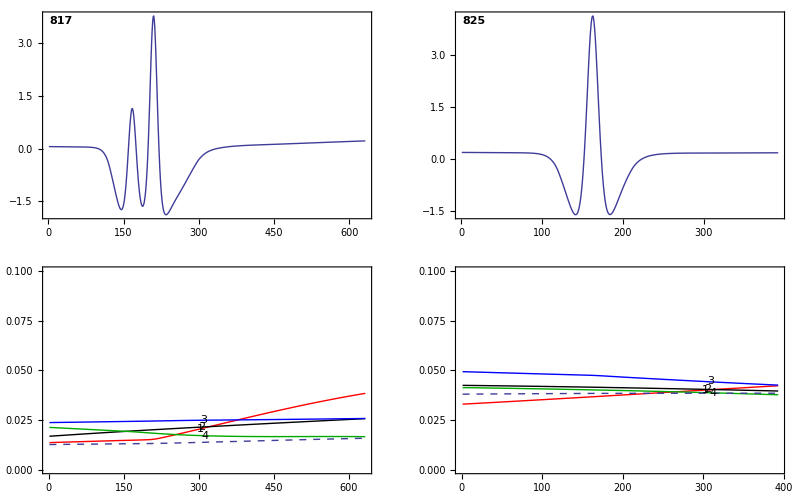

```mathematica
GraphicsGrid[{pedft,ppossq}ᵀ[[{5,9}]]ᵀ,ImageSize->Full]
```

```mathematica
Animate[Graphics3D[{Yellow,Sphere[#,.1]&/@pos[[i]],White,Table[Text[j,pos[[i,j]]],{j,16}],Gray, Sphere[posh[[i]],.05]}, PlotRange->{{-0.1,1.1},{-.1,1.1},{-.1,1.1}}],{i,1,Length[pos],1}]
```